```mathematica
GUASS[time_,delay_,sigma_]:=Exp[-0.5*((time-delay)/sigma)^2]
```

```mathematica
(*Mid infrared: 0.188 eV*)
```

```mathematica
tc=0.658;
500/tc
```

759.878

```mathematica
sigma=(100/(2.3548))
sigma=%/tc
```

42.4665

64.5387

```mathematica
durpump =(200/(2.3548)) (*sigma = 4.0 fs*)
durpump=%/tc
```

84.9329

129.077

```mathematica
t0 =250/tc
```

379.939

```mathematica
omega =0.207
```

0.207

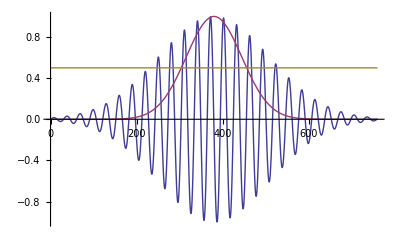

```mathematica
Plot[{GUASS[t,t0,durpump]*Sin[omega*t],GUASS[t,t0,sigma],0.5},{t,0,500/tc}]
```

```mathematica
tc=0.658;
150/tc
```

227.964

```mathematica
dur = 16.5/tc (*sigma = 16.5 fs*)
```

25.076

```mathematica
durpump =4/tc (*sigma = 4.0 fs*)
```

6.07903

```mathematica
t0 =75/tc
```

113.982

```mathematica
omega = 0.5
```

0.5

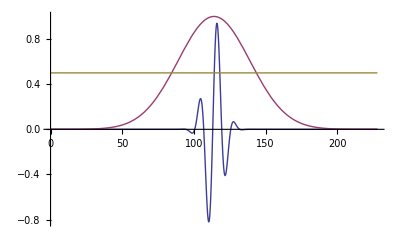

```mathematica
Plot[{GUASS[t,t0,durpump]*Sin[omega*t],GUASS[t,t0,dur],0.5},{t,0,150/tc}]
```

```mathematica
(*Mid infrared: 0.188 eV*)
```

```mathematica
tc=0.658;
800/tc
```

1215.81

```mathematica
2*Sqrt[2Log[2]]
```

2 √(2 Log[2])

```mathematica
sigma=(100/(2.3548))
```

42.4665

```mathematica
sigma=%/tc
```

64.5387

```mathematica
t0 =806
t1 =403
```

806

403

```mathematica
omega = 0.004
```

0.004

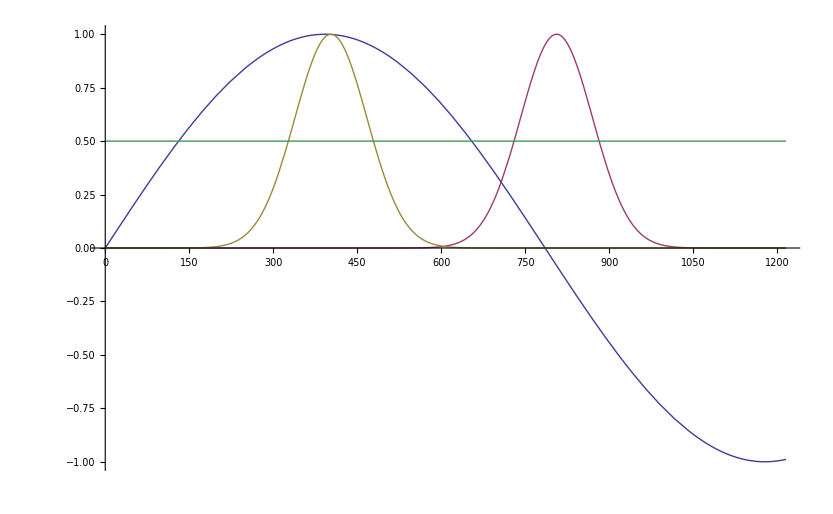

```mathematica
Plot[{Sin[omega*t],GUASS[t,t0,sigma],GUASS[t,t1,sigma],0.5},{t,0,800/tc}]
```

```mathematica
Integrate[1/(tt-tp)*Sin[0.1*t],{t,tt,tp}]/.{tt->10,tp->20}
Integrate[1/(tt-tp)*Sin[0.1*t],{t,tt,tp}]/.{tt->20,tp->10}
```

-0.956449

-0.956449

```mathematica
t1=.;
```

```mathematica
t0=.;
```

```mathematica
Expo[t1_,t2_]:=NIntegrate[-2*J0*Cos[k+1./(t1-t2)*NIntegrate[AA*Sin[ω*td],{td,t2,t1}]-AA*Sin[ω*tp]],{tp,t2,t1}]/.{ω->0.01,AA->0.5,J0->0.2,k->0.0}
```

```mathematica
Expo[100,110.]
```

NIntegrate::inumr: The integrand AA\ Sin[td\ ω] has evaluated to non-numerical values for all sampling points in the region with boundaries {{110., 100}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

3.9999

```mathematica
Series[Integrate[AA/(t1-t2)*Sin[ω*td],{td,t2,t1}]/.{t1->t2+eps},{eps,0,3}]
```

AA Sin[t2 ω]+1/2 AA ω Cos[t2 ω] eps-1/6 (AA ω^2 Sin[t2 ω]) eps^2-1/24 (AA ω^3 Cos[t2 ω]) eps^3+O[eps]^4

```mathematica
Series[Integrate[-2*J0*Cos[k+AA Sin[t2 ω]+1/2 AA ω Cos[t2 ω] eps-AA*Sin[ω*tp]],{tp,t2,t1}]/.{t1->t2+eps},{eps,0,2}]
```

-2 (J0 Cos[k]) eps+O[eps]^3

```mathematica
-2 eps J0 Cos[k]/.{ω->0.01,AA->10.0,J0->0.2,k->0.0,eps->10.}
```

-4.

```mathematica
Fermi[ω_,T_]:=1./(1.+Exp[ω/T])
```

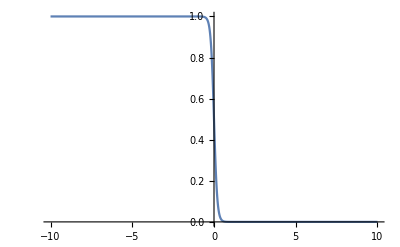

```mathematica
Plot[Fermi[w,0.1],{w,-10,10}]
```

```mathematica
Iphoto[k_,ω_,ω0_,t0_,eps_,T_,AA_,J0_]:=Im[I*Exp[+I*ω*eps]*Fermi[-2 J0 Cos[k+1/2 AA eps ω0 Cos[t0 ω0]+AA Sin[t0 ω0]],T]*Exp[I*2 eps J0 Cos[k]]]
```

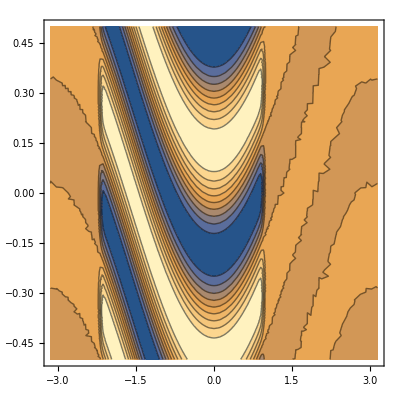

```mathematica
ContourPlot[{Iphoto[k,w,0.01,303.,10.0,0.01,10.0,0.25]},{k,-Pi,Pi},{w,-0.5,0.5}]
```

```mathematica
0.8225*400
```

329.

```mathematica
0.8225*100
```

82.25

```mathematica
(-100+51)*0.8225
```

-40.3025

```mathematica
Plot3D[{GUASS[t1,150,25]*GUASS[t2,150,25]},{t1,0,200},{t2,0,200},PlotRange->{0,10^-5}]
```

-Graphics3D-

```mathematica
Plot3D[{GUASS[t1,125,25]*GUASS[t2,125,25]},{t1,0,200},{t2,0,200},PlotRange->{0,1.0}]
```

-Graphics3D-